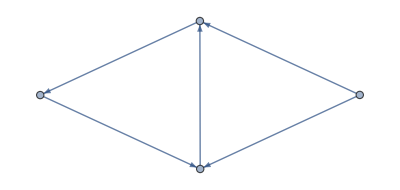

```mathematica
g = Graph[{A,B,C,D},{B->A,A->C,D->A,B->D,C->D}]
```

```mathematica
IncidenceMatrix[g] // MatrixForm
```

(1 | -1 | 1 | 0 | 0
-1 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | -1
0 | 0 | -1 | 1 | 1)

```mathematica
EdgeCycleMatrix[g] // MatrixForm
```

(0 | 1 | 1 | 0 | 1
-1 | 0 | 1 | 1 | 0)